# 2-frequency system

Wormholes:
Change Parameters
Comparing Approximations and Numerical

```mathematica
ClearAll[k1,k2,x,phi1,phi2,psi1,psi2,lambdac,h,h0,sol0,bFun,phase,a1,a2,h12,h12A,h12B,h12C,h12D,hA,hB,hC,hD,h12C,h12C,sol0,solA,solB,solC,solD,pltA]
```

```mathematica
imgsize=600;
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

Endpoint for NDSolve

```mathematica
endpoint=400
```

400

```mathematica
bFun[n1_,n2_,zk1_,zk2_,thetam_]:=Sin[2thetam]/4(-(-I)^(n1+n2))(2n1)BesselJ[n1,zk1]BesselJ[n2,zk2]
phase[n1_,n2_,phi1_,phi2_]:=Exp[I(n1 phi1+n2 phi2)]
```

```mathematica
h1[n1_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=k1/Cos[2thetam] bFun[n1,n2p,zk1,zk2,thetam]phase[n1,n2p,phi1,phi2]Exp[I(n1 k1+n2p k2-1)x]
h2[n2_,n1p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=k2/Cos[2thetam] bFun[n2,n1p,zk2,zk1,thetam]phase[n1p,n2,phi1,phi2]Exp[I(n1p k1+n2 k2-1)x]
```

I have n1 =1, n2=1, n1p=Round[(n2 k2 - 1)/k1], n2p=Round[(n1 k1 - 1)/k2],

```mathematica
thetamV=Pi/5;
k1V=0.35;
k2V=0.95;
a1V=0.1(k2V)^(-5/3);
a2V=0.1(k1V)^(-5/3);
zk1V=a1V Cos[2thetamV]/k1V;
zk2V=a2V Cos[2thetamV]/k2V;
phi1V=0;
phi2V=0;
init={psi1[0],psi2[0]}=={1,0};
```

```mathematica
Print[a1V,a2V]
```

0.1089250.57529

```mathematica
n101=Round[1/k1V];
n201=Round[(1-n101 k1V)/k2V];
n202=Round[1/k2V];
n102=Round[(1-n202 k2V)/k1V];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1V)/k2V];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2V)/k1V];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1V)/k2V];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1V)/k2V];
```

## Numerical Calculations Without Approximations

Solve the complete hamiltonian

```mathematica
hN[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=(a1 Sin[k1 x+phi1]+a2 Sin[k2 x+phi2])Sin[2thetam]Exp[I(-x-Cos[2thetam](a1/k1 Cos[k1 x+phi1]+a2/k2 Cos[k2 x+phi2]))]/2;
```

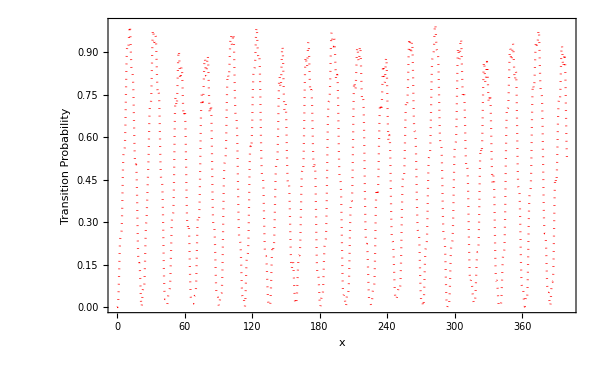

```mathematica
solN=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hN[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]},{Conjugate[hN[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

pltN=Plot[Evaluate[Abs[psi2[x]]^2/.solN],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->{Dotted,Red}]
```

## Approximations

“Most Important” Terms

Include only the “most important” term in the series

```mathematica
h0[k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n101,n201,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n202,n102,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

```mathematica
(*zk=a Cos[2 thetam]/k*)
```

```mathematica
h0S[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=h0[k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x]
(*h[1,1,Round[( k2-1)/k1],Round[(k1-1)/k2],k1,k2,a1,a2,a1 Cos[2thetam]/k1,a2 Cos[2thetam]/k2,phi1,phi2,thetam,x]*)
```

```mathematica
(*DSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12[k1,k2,a1,a2,phi1,phi2,thetam,x]},{Conjugate[h12[k1,k2,a1,a2,phi1,phi2,thetam,x]],0}}.{psi1[x],psi2[x]},{psi1,psi2},x]//FullSimplify*)
```

```mathematica
Re@h0S[0.95,1.03,0.1,0.2,0,0,Pi/5,4] (*Test the function*)
Re@h0S[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,4]
```

-0.0175627

0.0269992

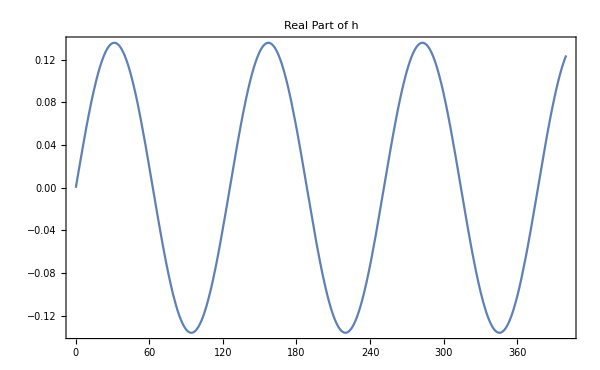

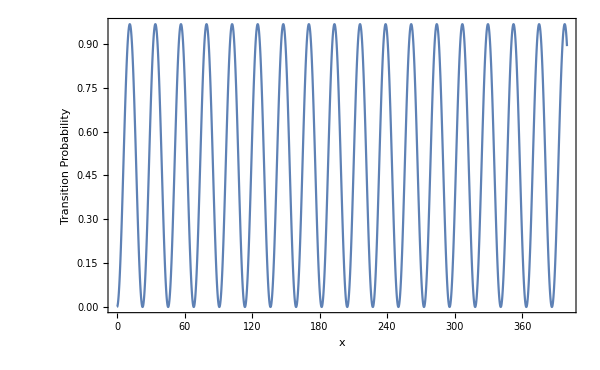

```mathematica
plt0Re=Plot[Re[h0S[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

h0SS[x_]:=h0S[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];

sol0=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h0SS[x]},{Conjugate[h0SS[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

plt0=Plot[Evaluate[Abs[psi2[x]]^2/.sol0],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Add Corrections of First Frequency

```mathematica
h01[x_]:=h0[k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h1[n1p1,n2p1,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h1[n1m1,n2m1,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x];
```

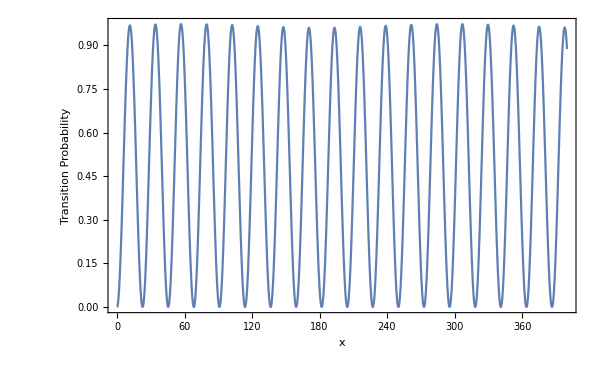

```mathematica
sol01=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h01[x]},{Conjugate[h01[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

plt01=Plot[Evaluate[Abs[psi2[x]]^2/.sol01],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Add Corrections of Second Frequency

```mathematica
h02[x_]:=h0[k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h2[n2p2,n1p2,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h2[n2m2,n1m2,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x];
```

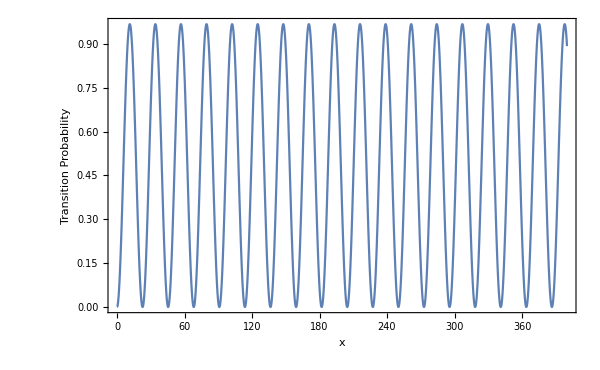

```mathematica
sol02=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h02[x]},{Conjugate[h02[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

plt02=Plot[Evaluate[Abs[psi2[x]]^2/.sol02],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Add Corrections of Both Frequencies

```mathematica
h012[x_]:=h0[k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h2[n2p2,n1p2,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h2[n2m2,n1m2,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h1[n1p1,n2p1,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x]+h1[n1m1,n2m1,k1V,k2V,a1V,a2V,zk1V,zk2V,phi1V,phi2V,thetamV,x];
```

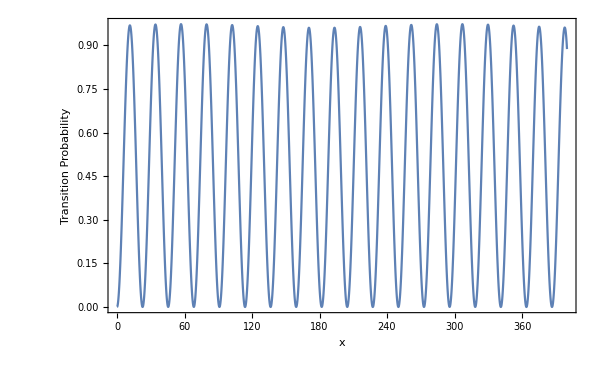

```mathematica
sol012=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h012[x]},{Conjugate[h012[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

plt012=Plot[Evaluate[Abs[psi2[x]]^2/.sol012],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

Comparing Approximations and Numerical

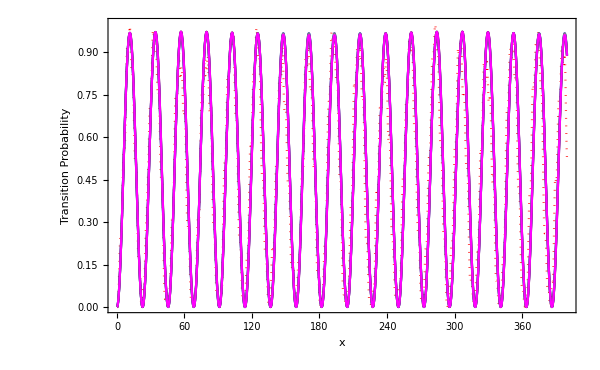

```mathematica
colN=Cases[plt0,_RGBColor,Infinity][[1]];
col0=Cases[plt0,_RGBColor,Infinity][[1]];
col01=Cases[plt01,_RGBColor,Infinity][[1]];
col02=Cases[plt02,_RGBColor,Infinity][[1]];
col012=Cases[plt012,_RGBColor,Infinity][[1]];
compApproxNum=Show[pltN,plt0/.col0->Blue,plt01/.col01->Black,plt02/.col02->Gray,plt012/.col012->Magenta,PlotRange->All]
(*Why do plt0 and plt01 overlap?*)
```

```mathematica
(*Export["export/compApproxNum/compApproxNum-RkL-AmpL.png",compApproxNum]*)
```

export/compApproxNum/compApproxNum-RkL-AmpL.png

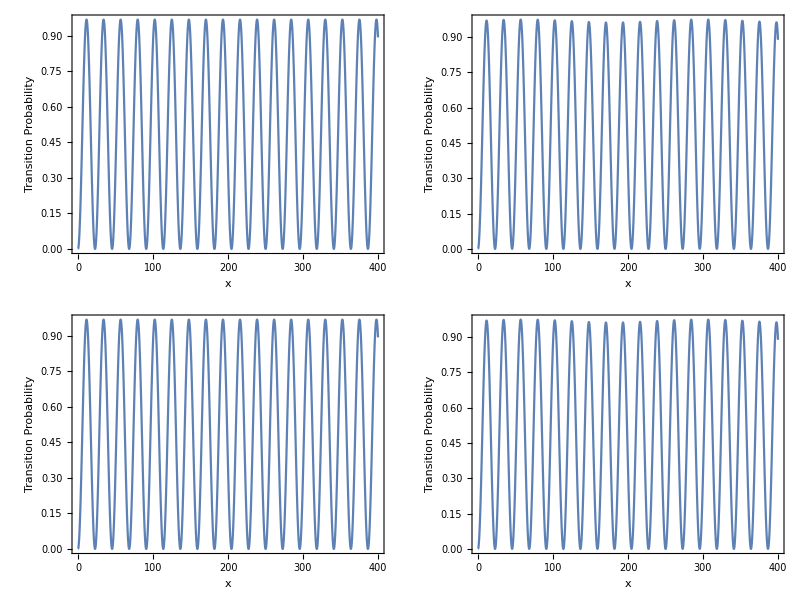

```mathematica
Grid[{{plt0,plt01},{plt02,plt012}}]
```

```mathematica
Grid[{{Show[Import["export/compApproxNum/compApproxNum-RkS-AmpS.png"],ImageSize->imgsize],Show[Import["export/compApproxNum/compApproxNum-RkS-AmpL.png"],ImageSize->imgsize]},{Show[Import["export/compApproxNum/compApproxNum-RkL-AmpS.png"],ImageSize->imgsize],Show[Import["export/compApproxNum/compApproxNum-RkL-AmpL.png"],ImageSize->imgsize]}}]
(*Export["export/compApproxNum/compApproxNum.png",%]*)
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

export/compApproxNum/compApproxNum.png

## Analytical

Solve the equation of motion for lowest order

```mathematica
(*ClearAll[sys,psi,psi1,psi2,k,fact1R,fact1I,fact2R,fact2I,helem]
helem=(fact1R+I fact1I)Exp[I(n1 k1+k2p k2 -1)x]+(fact2R+I fact2I)Exp[I(n1p k1+k2 k2 -1)x]
helemConj=(fact1R-I fact1I)Exp[-I(n1 k1+k2p k2 -1)x]+(fact2R-I fact2I)Exp[-I(n1p k1+k2 k2 -1)x]
sys = I D[{psi1[x],psi2[x]},x]=={{0,helem},{helemConj,0}}.{psi1[x],psi2[x]}
DSolve[sys,{psi1,psi2},x]//FullSimplify*)
```